# Frank model with thermodynamical consistency

```mathematica
Styles={PlotTheme->{"Scientific","DashedLines"},PlotTheme->{"Scientific","DashedLines"},LabelStyle->Directive[FontFamily->"Helvetica",Black,FontSize->20],FrameStyle->Directive[Black,FontSize->20,Thickness[.003]]};
```

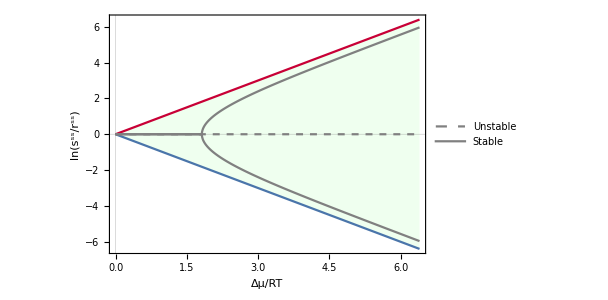

```mathematica
GetSol[a_,m_,Keq1_,Keq2_,k0_]:=Module[{sol},sol=NSolve[{0==r (a-Keq1 r)+k0 (Keq2 m-r s),0==s (a-Keq1 s)+k0 (Keq2 m-r s)},{r,s},Reals];
Select[sol,(r>0/. #)&&(s>0/. #)&]]
mlist = Table[i,{i,0.1,3,0.01}];
With[{a = 5,
Keq1=0.7,
Keq2=8.5,
k0=2,
dm=0.01},
mmax=1/(Keq1^2 Keq2/a^2);
Aelist = Reverse@Table[-Log[Keq1^2 Keq2*m/a^2 ],{m,0.01,mmax,dm}];
chlist=Reverse@Table[Log[s/r]/.GetSol[a,m,Keq1,Keq2,k0][[1]],{m,0.01,mmax,dm}];
unstablelist=Reverse@Table[0,{m,0.01,mmax,dm}];
Show[
ListPlot[{Transpose@{Aelist,-Aelist},Transpose@{Aelist,Aelist}},Joined->True,Filling->{1->{2}},PlotStyle->{{RGBColor["#4A75AA"]},{RGBColor["#C80036"]}},
FillingStyle->Directive[Opacity[0.5],LightGreen], 
FrameLabel->{"Δμ/RT","ln(s^ss/r^ss)"},
FrameStyle->Directive[Black,FontSize->20,Thickness[.004/3*2]],PlotStyle->Red,AxesLabel->{"m","log(s/r)"},PlotRange->Full,Evaluate@Styles,AspectRatio->2/3],
ListPlot[{Transpose@{Aelist,-unstablelist},Transpose@{Aelist,chlist},Transpose@{Aelist,-chlist}},PlotLegends->Placed[{"Unstable","Stable"},{0.2,0.85}],Joined->True,PlotStyle->{{Gray,Dashed},{Gray},{Gray}},PlotStyle->PointSize[Medium],AxesLabel->{"m","log(s/r)"},PlotRange-> Full,Evaluate@Styles],ImageSize->300*3/2
 
]
]
```

```mathematica
Manipulate[Module[{drdt,dsdt,fixedPoints,stream,contourR,contourS,tspace},
drdt= r (a-Keq1 r)+k0(Keq2 m-r s);
dsdt= s (a-Keq1 s)+k0(Keq2 m-r s);
(*Solve for fixed points numerically*)
fixedPoints=Quiet@N[Solve[{drdt==0,dsdt==0},{r,s},Reals]/. {a->a,k0->k0,Keq1->Keq1,Keq2->Keq2,m->m}];
(*Plot nullclines*)
contourR=ContourPlot[drdt==0,{r,0,xmax},{s,0,xmax},ContourStyle->{RGBColor["#E29000"]},
Contours->{0},
PlotLabel->Log[Keq1^2 Keq2*m/a^2 ],
ContourLabels->(Text["dr/dt = 0",#,Background->White,FontSize->12]&)];
contourS=ContourPlot[dsdt==0,{r,0,xmax},{s,0,xmax},ContourStyle->{RGBColor["#127475"]}];
(*Stream plot*)
stream=StreamPlot[{drdt,dsdt},{r,0,xmax},{s,0,xmax},StreamStyle->Gray,StreamColorFunction->None];
(*Optional:shaded region from your tspace*)
tspace=Plot[{Keq1^2 Keq2*m/a^2 s,s/(Keq1^2 Keq2*m/a^2)},{s,0,10},PlotRange->{{0,10},{0,10}},
PlotStyle->{{RGBColor["#4A75AA"]},{RGBColor["#C80036"]}},
Filling->{1->{2}},FillingStyle->Directive[Opacity[0.08],Green]];
Show[contourR,contourS,tspace,stream,
Graphics[{Orange,Thick,Circle[{#[[1]],#[[2]]},0.1]&/@({r,s}/. fixedPoints)}],
FrameLabel->{"r","s"},
LabelStyle->Directive[FontFamily->"Helvetica",Black,FontSize->20],FrameStyle->Directive[Black,FontSize->20,Thickness[.004]],
ImageSize->300
]
],(*Controls*)
{{k0,2},0.01,100,Appearance->"Labeled"},
{{Keq1,0.7},0.01,10,Appearance->"Labeled"},
{{xmax,6.5},0.01,20,Appearance->"Labeled"},
{{Keq2,8.5},0.01,10,Appearance->"Labeled"},
{{a,5},0,20,Appearance->"Labeled"},
{{m,0.5},0,10,Appearance->"Labeled"}]
```